```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Medium,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[MatrixPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[Plot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black}];
SetOptions[ParametricPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->19}];
SetOptions[ListPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black},PlotMarkers->None,Filling->Axis];
```

The simple harmonic, undamped, unforced pendulum, its recurrence plot and DFT are calculated.  In the DFT, a threshold value of 10% is used,  In essence, only those frequencies are plotted that make up 10% or more of the total spectral energy.

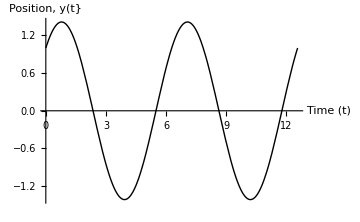

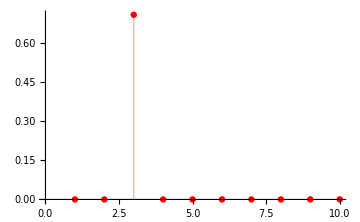

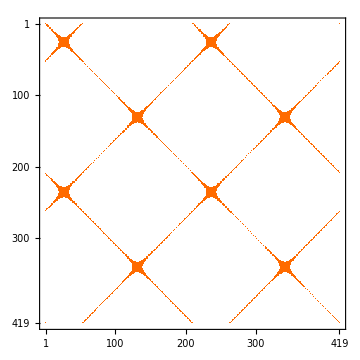

```mathematica
{δ,y,t,s,tmax=4π};
s=NDSolveValue[{y''[t]+y[t]==0.,y[0]==1,y'[0]==1},y,{t,0,tmax}];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]

data=Table[s[t],{t,0,tmax,tmax/200}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=0.1Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]];
ListPlot[f[[1;;10]],ImageSize->Medium]


MatrixPlot[UnitStep[0.001-DistanceMatrix[s[Range[0,tmax,0.03]]]]]

(*FData1=Abs[Fourier[UnitStep[0.1-DistanceMatrix[s[Range[0,tmax,0.05]]]]]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh1=0.8Max[FData2];
FData=Threshold[FData2,{"Hard",thresh1}];
d=Dimensions[FData][[1]];

MatrixPlot[FData[[1;;Ceiling[d/20],1;;Ceiling[d/20]]],BaseStyle->{FontWeight->"Plain",FontSize->25},PlotLegends->Automatic,FrameTicks->All]*)
```

A damped oscillator that is unforced is now simulated.  Its recurrence plot and DFT are calculated.  In the DFT, a threshold value of 10% is used,  In essence, only those frequencies are plotted that make up 10% or more of the total spectral energy.

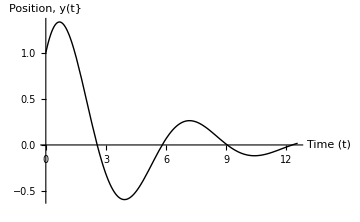

201

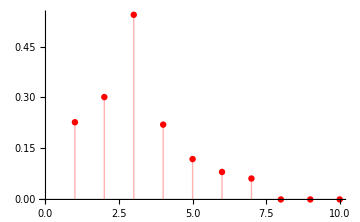

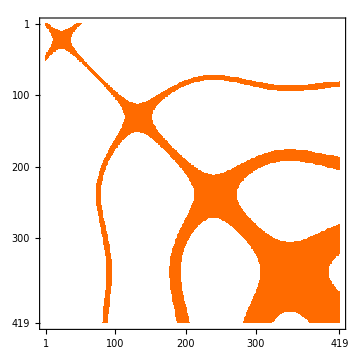

```mathematica
{δ,y,t,s,tmax=4π};
s=NDSolveValue[{y''[t]+0.5y'[t]+y[t]==0.,y[0]==1,y'[0]==1},y,{t,0,tmax}];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]

data=Table[s[t],{t,0,tmax,tmax/200}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=0.1Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]]
ListPlot[f[[1;;10]],ImageSize->Medium]
MatrixPlot[UnitStep[0.01-DistanceMatrix[s[Range[0,tmax,0.03]]]]]

(*FData1=Abs[Fourier[UnitStep[0.1-DistanceMatrix[s[Range[0,tmax,tmax/50]]]]]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh1=0.7Max[FData2];
FData=Threshold[FData2,{"Hard",thresh1}];
d=Dimensions[FData][[1]];

MatrixPlot[FData[[1;;Ceiling[d/4],1;;Ceiling[d/4]]],BaseStyle->{FontWeight->"Plain",FontSize->25},PlotLegends->Automatic,FrameTicks->All]*)
```

A damped oscillator, with a forcing function is now simulated.  TIts recurrence plot and DFT are calculated.  In the DFT, a threshold value of 10% is used,  In essence, only those frequencies are plotted that make up 10% or more of the total spectral energy.

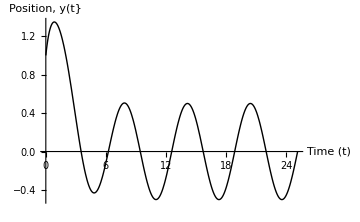

201

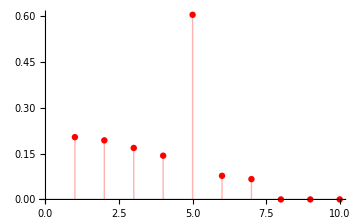

-Graphics-

```mathematica
{δ,y,t,s,tmax=8π};
s=NDSolveValue[{y''[t]+2y'[t]+y[t]==Cos[t],y[0]==1,y'[0]==1},y,{t,0,tmax}];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"}]

data=Table[s[t],{t,0,tmax,tmax/200}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=0.1Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]]
ListPlot[f[[1;;10]],ImageSize->Medium]

MatrixPlot[UnitStep[0.01-DistanceMatrix[s[Range[0,tmax,0.03]]]]]
(*FData1=Abs[Fourier[UnitStep[0.1-DistanceMatrix[s[Range[0,tmax,tmax/50]]]]]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh1=0.7Max[FData2];
FData=Threshold[FData2,{"Hard",thresh1}];
d=Dimensions[FData][[1]];

MatrixPlot[FData[[1;;Ceiling[d/4],1;;Ceiling[d/4]]],BaseStyle->{FontWeight->"Plain",FontSize->25},PlotLegends->Automatic,FrameTicks->All]*)
```

Adaptation from example problem from Speigel’s Schaum’s series: Theory and Problems of Classical Mechanics

A vertical spring has stiffness factor 16.  If forced with a forcing function of 30 Cos[6 t], plot the position in time.

This is an undamped oscillator with a forcing function.  Not only is the equation for position solved as a differential equation, its position is tracked in time.  In addition to this, I turn “ON” damping at a certain time (for t>5π) and track its effect through the use of a recurrence plot.

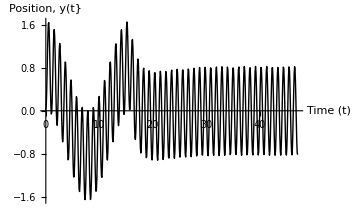

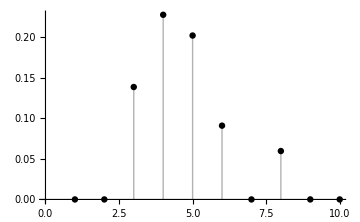

-Graphics- -Graphics-

```mathematica
tmax=15π;
s=NDSolveValue[{y''[t]+δ[t] y'[t]+.16y[t]==30Cos[6t],y[0]==0,y'[0]==0,δ[0]== 0.,WhenEvent[t>5π,δ[t]->.9]},y,{t,0,tmax},DiscreteVariables->δ];
Plot[s[t],{t,0,tmax},AxesLabel->{"Time (t)","Position, y(t}"},PlotPoints->10]

data=Table[s[t],{t,0,tmax,tmax/200}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=0.1Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]];
ListPlot[f[[1;;10]],ImageSize->Medium]

With[{stepSize=tmax/10,end=tmax},
MatrixPlot[UnitStep[0.1-DistanceMatrix[s[Range[0,15π,tmax/1000]]]]]
MatrixPlot[UnitStep[0.1-DistanceMatrix[s[Range[30π,tmax,stepSize]]]]]
]

(*FData1=Abs[Fourier[UnitStep[0.1-DistanceMatrix[s[Range[0,tmax,tmax/50]]]]]];
FData1[[1,1]]=0;
norm1=Norm[FData1,"Frobenius"];
FData2=FData1/norm1;
thresh1=0.7Max[FData2];
FData=Threshold[FData2,{"Hard",thresh1}];
d=Dimensions[FData][[1]];

MatrixPlot[FData[[1;;Ceiling[d/4],1;;Ceiling[d/4]]],BaseStyle->{FontWeight->"Plain",FontSize->25},PlotLegends->Automatic,FrameTicks->All]*)
```

This analysis method is now used for the 4th order non-linear evolution equation that models a liquid film on an isothermal substrate.  The substrate may either be non-porous (base case) or have a uniformly saturated porosity.  The main interest is the film dynamics in zero gravity with and without a porous substrate, when the film is destabilized by thermocapillarity.

```mathematica
{j=2.,k = 0.0677,xMin=0,xMax=j*(Pi/k),TMax1=2000.,TMax2=4000.,Bi=1.,M,Pr=7.02, Ga=0.,Pm=0.25};
mult=0.;
M=5;
S=100;
hSol= NDSolveValue[{D[u[t, x], t] == (-S)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         M*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax1}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}];

mult=1.;
M=5;
S=100;
hSolp= NDSolveValue[{D[u[t, x], t] == (-S)*D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
         M*D[(u[t, x]/(1 + Bi*u[t, x]))^2*D[u[t, x], x], x] + mult*Pm*D[u[t, x], x, x], u[0, x] == 1 + 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
        Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
        Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax2}, {x, xMin, xMax}, MaxSteps -> 100000, PrecisionGoal->10,
       Method -> {"MethodOfLines", "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
          {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, "DifferenceOrder" -> 5}}];
```

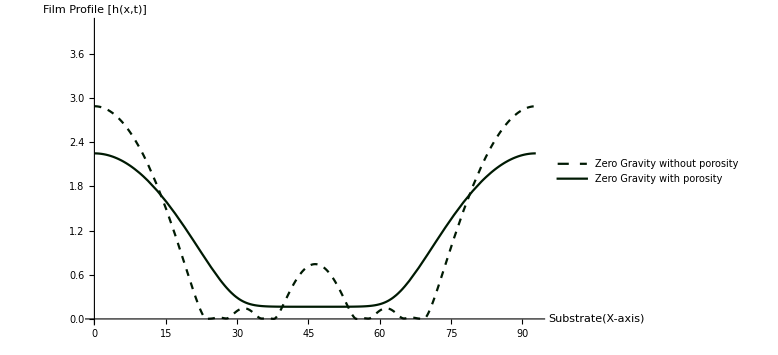

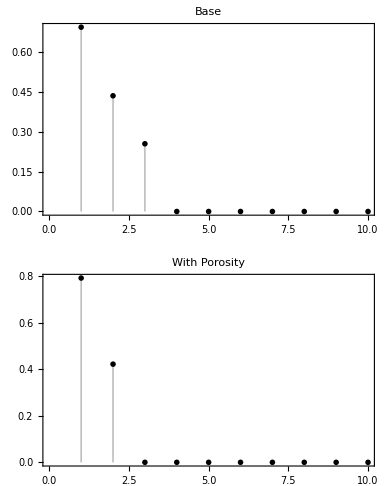

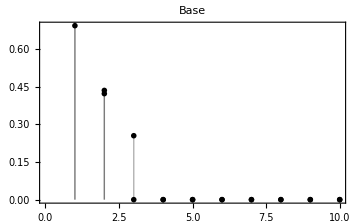

```mathematica
p1=Plot[{hSol[TMax1,x],hSolp[TMax2,x]},{x,xMin,xMax},PlotRange->{0,4},BaseStyle->{FontWeight->"Bold",FontSize->14},AxesLabel->{"Substrate(X-axis)","Film Profile [h(x,t)]"},ImageSize->Large,PlotStyle->{{Thick,Dashed,RGBColor[0.,0.1,0.01]},{Thick,RGBColor[0.,0.1,0.01]}},PlotLegends->{"Zero Gravity without porosity","Zero Gravity with porosity"}]


valThresh=0.1;
data=Table[hSol[TMax1,x],{x,xMin,xMax,(xMax-xMin)/100}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=valThresh Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]];
p2=ListPlot[f[[1;;10]],ImageSize->Medium,PlotLabel->"Base",Frame->True,PlotStyle->{Thick,Black,Large},PlotMarkers->{"*",26}];


data=Table[hSolp[TMax1,x],{x,xMin,xMax,(xMax-xMin)/100}];
f1=Abs[Fourier[data]];
norm1=Norm[f1,"Frobenius"];
f2=f1/norm1;
thresh1=valThresh Max[f2];
f=Threshold[f2,{"Hard",thresh1}];
d=Dimensions[f][[1]];
p3=ListPlot[f[[1;;10]],ImageSize->Medium,PlotLabel->"With Porosity",Frame->True,PlotMarkers->{"o",16}];
GraphicsGrid[{{p2},{p3}}]
Show[p2,p3]
```

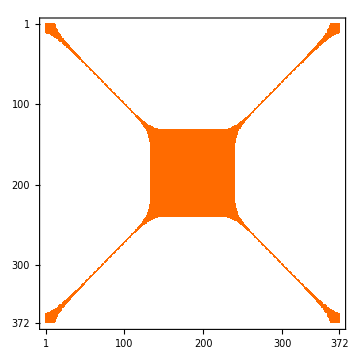
-Graphics- -Graphics-

```mathematica
With[{stepSize=0.25,end=xMax,fraction=1.},
MatrixPlot[UnitStep[0.001-DistanceMatrix[hSol[fraction TMax1,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome"]
MatrixPlot[UnitStep[0.001-DistanceMatrix[hSolp[fraction TMax2,Range[xMin,end,stepSize]]]]]
]
```

Linear stability analysis, trajectories and phase portraits.

```mathematica
Clear[Ga,Sn,Bi,Pm,m,ω,t,q,x,H0,H,θ];
H=H0 Exp[ω t+I q x];
D[H,t]+Sn D[H,x,x,x,x]-(Ga/3) D[H,x,x]+(m/(1+Bi)^2) D[H,x,x]-Pm (D[H,x,x]-Ga H)/.Exp[ω t+I q x]->θ/(H0 θ);
gr=Solve[%==0,ω][[1]][[1]][[2]]

qmaxval=2;Bi=1.0;
Inactive[Manipulate[Plot[gr/.{Ga->xg 1./3.,Sn->xs 100.,Pm->xp 1/2,m->xm 5.},{q,0,qmaxval},PlotRange->{{0,qmaxval},{1,-0.0}},AxesLabel->{"wavenumber","Growth rate"},BaseStyle->{FontSize->18},PlotStyle->{Thick,Black},ImageSize->Large,GridLines->Automatic],{xg,0,20},{{xs,.6},0.1,10},{xp,0,5},{{xm,5},0,5}]]
```

-(Ga q^2)/3+(m q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn

Inactive[]

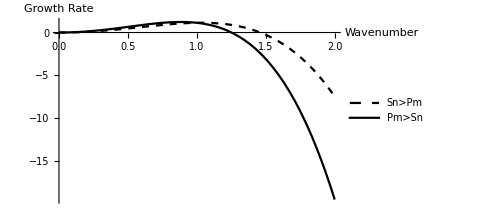

```mathematica
Clear[Ga,m,Pm,Sn,Bi];
gr1=gr/.{Ga->0,Bi->0.1, m->5,Sn->1,Pm->2};
gr2=gr/.{Ga->0,Bi->0.1, m->5,Sn->2,Pm->1};
Plot[{gr1,gr2},{q,0,2},PlotStyle->{{Dashed,Black},{Thick,Black}},AxesLabel->{"Wavenumber","Growth Rate"},PlotLegends->{"Sn>Pm","Pm>Sn"},PlotRange->All]
```

0.+4.13223 q^2-1. q^4

8.26446 q-4. q^3

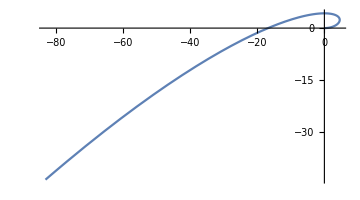

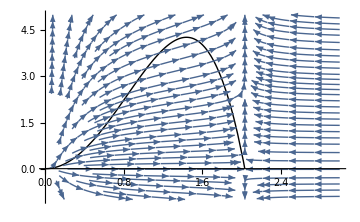

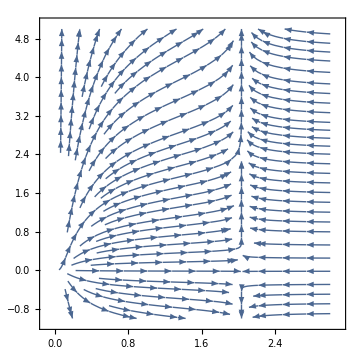

```mathematica
Sn=1.;Pm=0.;qmaxlimit=3.;
ω=4.132231404958677 q^2-Pm q^2-q^4 Sn
dω=D[ω,q]
ParametricPlot[{dω,ω},{q,0,qmaxlimit}]
Show[Plot[ω,{q,0,qmaxlimit},PlotRange->{{0,3},{5,0}}],
StreamPlot[{4.132231404958677 q^2-Pm q^2-q^4 Sn,y},{q,0,qmaxlimit},{y,-1,5},VectorScale->{Large,0.35}]]
StreamPlot[{4.132231404958677 q^2-Pm q^2-q^4 Sn,y},{q,0,qmaxlimit},{y,-1,5},VectorScale->{Large,0.35}]
```

3.13223 q^2-1. q^4

6.26446 q-4. q^3

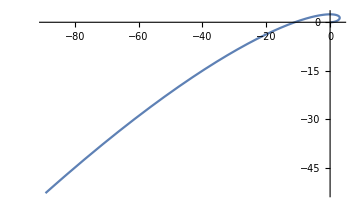

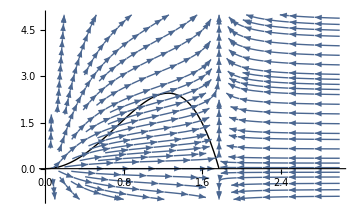

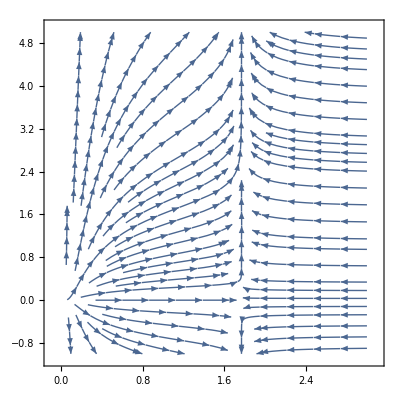

```mathematica
Sn=1.;Pm=1.;qmaxlimit=3;
ω=4.132231404958677 q^2-Pm q^2-q^4 Sn
dω=D[ω,q]
ParametricPlot[{dω,ω},{q,0,qmaxlimit}]
Show[Plot[ω,{q,0,qmaxlimit},PlotRange->{{0,3},{5,0}}],
StreamPlot[{4.132231404958677 q^2-Pm q^2-q^4 Sn,y},{q,0,qmaxlimit},{y,-1,5},VectorScale->{Large,0.35}]]
StreamPlot[{4.132231404958677 q^2-Pm q^2-q^4 Sn,y},{q,0,qmaxlimit},{y,-1,5},VectorScale->{Large,0.35}]
```

Comparison of growth rate, with and without Porosity

4.13223 q^2-1. q^4

3.13223 q^2-1. q^4

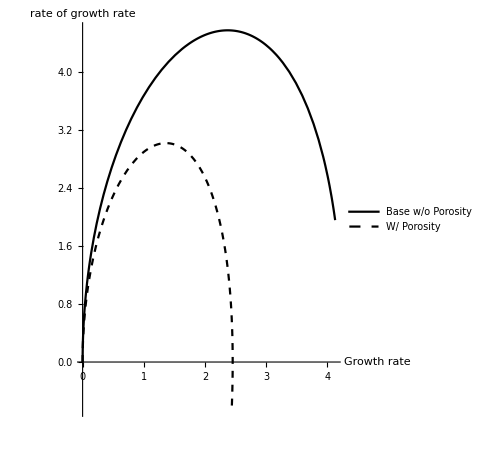

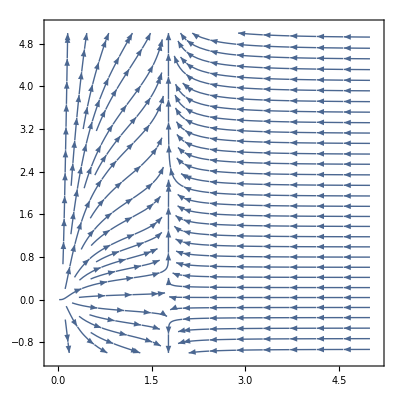

```mathematica
Clear[q,Pm,S,qmaxlimit];
qmaxlimit=1.3;
S=1;Pm=0;
ω1=4.132231404958677 q^2-Pm q^2-q^4 Sn
dω1=D[ω1,q];
S=1;Pm=1;
ω2=4.132231404958677 q^2-Pm q^2-q^4 Sn
dω2=D[ω2,q];
ParametricPlot[{{ω1,dω1},{ω2,dω2}},{q,0,qmaxlimit},PlotStyle->{{Thick,Black},{Thick,Dashed,Black}},AxesLabel->{"Growth rate","rate of growth rate"},PlotLegends->{"Base w/o Porosity","W/ Porosity"}]
StreamPlot[{4.132231404958677 q^2-Pm q^2-q^4 Sn,y},{q,0,5},{y,-1,5},VectorScale->{Large,0.35}]
```

Response diagram of the growth rate equation

(4.13223 q^2-Pm q^2-q^4 Sn)/Sn

-q^4+(4.13223 q^2)/Sn-(Pm q^2)/Sn

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q→0.},{q→0.},{q→-(0.0909091 √(500.-121. Pm))/(√Sn)},{q→(0.0909091 √(500.-121. Pm))/(√Sn)}}

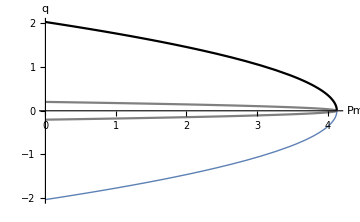

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;

M=5;Bi=0.1;Ga=0;
ff=f/Sn
Expand[ff]
Solve[ff==0,q]

Show[Sn=100.;

Plot[{-(0.09090909090909091 √(500.-121. Pm))/(√Sn),(0.09090909090909091 √(500.-121. Pm))/(√Sn)},{Pm,0,10},AxesLabel->{"Pm","q"},PlotRange->All,PlotStyle->Gray],

Sn=1.;
Plot[{-(0.09090909090909091 √(500.-121. Pm))/(√Sn),(0.09090909090909091 √(500.-121. Pm))/(√Sn)},{Pm,0,10},AxesLabel->{"Pm","q"}],PlotRange->All,PlotStyle->Gray]
```

```mathematica
Pm=0.025;
Show[ParametricPlot[{ff,dff},{q,-10,10},PlotStyle->{Thick,Black}],
StreamPlot[{ff,y},{q,-10000,1000},{y,-5000,5000}]]
```